```mathematica
Exit
```

```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/Jerry/Documents/git/AmplitudeBasis

```mathematica
$DEBUG=True;
<<AmplitudeBasis`
```

### Example

#### SMEFT

```mathematica
(* Presented Indices *)
SU3ADJ=ToUpperCase/@Alphabet[][[1;;8]];
SU3FUND=Alphabet[];
SU2ADJ=ToUpperCase/@DeleteCases[Alphabet[][[9;;-1]],"l"];
SU2FUND=Alphabet[][[9;;-1]];
```

```mathematica
(* Define SMEFT *)
SetAttributes[DefSMEFT,HoldFirst];
DefSMEFT[model_,nf_:3]:=Module[{},
model=<|"Global"->{"Baryon","Lepton"},"rep2ind"-><||>,"rep2indOut"-><||>|>;
AddGroup[model,"SU3c","G",{0,0},<|{0,0}->{Function[x,Nothing],{}},{1,0}->{b,SU3FUND},{0,1}->{b,SU3FUND},{1,1}->{B,SU3ADJ}|>];
AddGroup[model,"SU2w","W",{0,0},<|{0}->{Function[x,Nothing],{}},{1}->{a,SU2FUND},{2}->{A,SU2ADJ}|>];
AddGroup[model,"U1y","B",{0,0},<||>];
AddField[model,"Q",-1/2,{{1,0},{1},1/6},{1/3,0},Flavor->nf,Chirality->{"q","left"}];
AddField[model,"uc",-1/2,{{0,1},{0},-2/3},{-1/3,0},Flavor->nf,Chirality->{"u","right"}];
AddField[model,"dc",-1/2,{{0,1},{0},1/3},{-1/3,0},Flavor->nf,Chirality->{"d","right"}];
AddField[model,"L",-1/2,{{0,0},{1},-1/2},{0,1},Flavor->nf,Chirality->{"l","left"}];
AddField[model,"ec",-1/2,{{0,0},{0},1},{0,-1},Flavor->nf,Chirality->{"e","right"}];
AddField[model,"H",0,{{0,0},{1},1/2},{0,0}]
]
```

```mathematica
DefSMEFT[Model,nf];
```

```mathematica
Type2TermsPro[Model,("uc")^2("dc")^4,deSym->False,fullform->True]
```

<|m-basis→{ϵ_ace^ϵ_bdf^ (dc_^a dc_^b) (dc_^c dc_^d) (uc_^e uc_^f),ϵ_ace^ϵ_bdf^ (dc_^a dc_^b) (dc_^c uc_^e) (dc_^d uc_^f),ϵ_ace^ϵ_bdf^ (dc_^a dc_^c) (dc_^b dc_^d) (uc_^e uc_^f),ϵ_ace^ϵ_bdf^ (dc_^a dc_^c) (dc_^b uc_^e) (dc_^d uc_^f),ϵ_ace^ϵ_bdf^ (dc_^a dc_^d) (dc_^b uc_^e) (dc_^c uc_^f),ϵ_aef^ϵ_bcd^ (dc_^a dc_^b) (dc_^c dc_^d) (uc_^e uc_^f),ϵ_aef^ϵ_bcd^ (dc_^a dc_^b) (dc_^c uc_^e) (dc_^d uc_^f),ϵ_aef^ϵ_bcd^ (dc_^a dc_^c) (dc_^b dc_^d) (uc_^e uc_^f),ϵ_aef^ϵ_bcd^ (dc_^a dc_^c) (dc_^b uc_^e) (dc_^d uc_^f),ϵ_aef^ϵ_bcd^ (dc_^a dc_^d) (dc_^b uc_^e) (dc_^c uc_^f),-ϵ_abd^ϵ_cef^ (dc_^a dc_^b) (dc_^c dc_^d) (uc_^e uc_^f),-ϵ_abd^ϵ_cef^ (dc_^a dc_^b) (dc_^c uc_^e) (dc_^d uc_^f),-ϵ_abd^ϵ_cef^ (dc_^a dc_^c) (dc_^b dc_^d) (uc_^e uc_^f),-ϵ_abd^ϵ_cef^ (dc_^a dc_^c) (dc_^b uc_^e) (dc_^d uc_^f),-ϵ_abd^ϵ_cef^ (dc_^a dc_^d) (dc_^b uc_^e) (dc_^c uc_^f),ϵ_adf^ϵ_bce^ (dc_^a dc_^b) (dc_^c dc_^d) (uc_^e uc_^f),ϵ_adf^ϵ_bce^ (dc_^a dc_^b) (dc_^c uc_^e) (dc_^d uc_^f),ϵ_adf^ϵ_bce^ (dc_^a dc_^c) (dc_^b dc_^d) (uc_^e uc_^f),ϵ_adf^ϵ_bce^ (dc_^a dc_^c) (dc_^b uc_^e) (dc_^d uc_^f),ϵ_adf^ϵ_bce^ (dc_^a dc_^d) (dc_^b uc_^e) (dc_^c uc_^f),ϵ_ade^ϵ_bcf^ (dc_^a dc_^b) (dc_^c dc_^d) (uc_^e uc_^f),ϵ_ade^ϵ_bcf^ (dc_^a dc_^b) (dc_^c uc_^e) (dc_^d uc_^f),ϵ_ade^ϵ_bcf^ (dc_^a dc_^c) (dc_^b dc_^d) (uc_^e uc_^f),ϵ_ade^ϵ_bcf^ (dc_^a dc_^c) (dc_^b uc_^e) (dc_^d uc_^f),ϵ_ade^ϵ_bcf^ (dc_^a dc_^d) (dc_^b uc_^e) (dc_^c uc_^f)},coordinate→<|{dc→{3,1},uc→{1,1}}→{{-1/8,1/16,-1/16,0,0,-1/4,1/8,-1/8,0,0,-1/8,1/16,-1/16,1/16,1/16,-1/4,1/8,-1/8,1/8,1/8,0,0,0,0,0},{0,-1/48,1/16,-1/24,1/24,0,0,0,0,0,0,1/48,1/16,-1/48,1/48,0,0,0,0,0,0,0,0,0,0}},{dc→{2,1,1},uc→{1,1}}→{{-1/6,1/12,-1/12,1/24,1/24,-1/12,1/24,-1/24,-1/24,-1/24,0,0,0,0,0,1/4,-1/8,1/8,-1/8,-1/8,1/4,-1/8,1/8,-1/8,-1/8},{0,0,0,1/16,-1/16,0,0,0,0,0,0,-1/16,1/16,1/16,-1/16,0,0,0,0,0,0,0,0,0,0}},{dc→{4},uc→{2}}→{{0,1/24,1/24,-1/12,1/12,0,0,1/12,-1/12,1/12,0,1/24,1/24,-1/24,1/24,0,0,1/12,0,0,0,-1/12,0,1/12,-1/12},{-1/3,1/6,-1/6,0,0,0,0,0,0,0,-1/3,1/6,-1/6,1/6,1/6,0,0,0,0,0,0,0,0,0,0}},{dc→{3,1},uc→{2}}→{{0,-3/64,1/64,1/32,-1/32,0,-1/32,1/32,0,0,0,-1/64,1/64,1/64,-1/64,0,1/32,1/32,-1/32,1/32,0,1/16,0,-1/16,1/16}},{dc→{2,2},uc→{2}}→{{0,1/24,1/24,-1/48,1/48,0,1/16,1/48,-1/48,1/48,0,1/24,1/24,-1/24,1/24,0,1/16,1/48,-1/16,1/16,0,-1/48,-1/16,1/48,-1/48},{0,0,0,1/9,1/9,0,0,0,0,0,-2/9,1/9,-1/9,1/9,1/9,0,0,0,0,0,0,0,0,0,0}},{dc→{2,1,1},uc→{2}}→{{0,0,1/16,0,0,0,-1/32,1/32,1/32,-1/32,0,-1/32,1/32,1/32,-1/32,0,-3/32,-1/32,3/32,-3/32,0,-1/32,-3/32,1/32,-1/32}},{dc→{1,1,1,1},uc→{2}}→{{2/9,-1/9,1/9,-2/9,-2/9,0,0,0,0,0,-2/9,1/9,-1/9,-1/9,-1/9,0,0,0,0,0,0,0,0,0,0}}|>|>

```mathematica
Length/@%["coordinate"]
```

<|{dc→{3,1},uc→{1,1}}→2,{dc→{2,1,1},uc→{1,1}}→2,{dc→{4},uc→{2}}→2,{dc→{3,1},uc→{2}}→1,{dc→{2,2},uc→{2}}→2,{dc→{2,1,1},uc→{2}}→1,{dc→{1,1,1,1},uc→{2}}→1|>

```mathematica
Type2TermsPro[Model,("Q")^4("dc†")^2,deSym->False,fullform->True]
```

<|m-basis→{ϵ_^aceϵ_^bdfϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^aceϵ_^bdfϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^aceϵ_^bdfϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^aceϵ_^bdfϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^acdϵ_^befϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^acdϵ_^befϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^acdϵ_^befϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^acdϵ_^befϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^abeϵ_^cdfϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^abeϵ_^cdfϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^abeϵ_^cdfϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^abeϵ_^cdfϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^abdϵ_^cefϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^abdϵ_^cefϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^abdϵ_^cefϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^abdϵ_^cefϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^abcϵ_^defϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^abcϵ_^defϵ_^ikϵ_^jl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^),ϵ_^abcϵ_^defϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_bj^) (Q_ck^ Q_dl^),ϵ_^abcϵ_^defϵ_^ijϵ_^kl ((dc†)_e^ (dc†)_f^) (Q_ai^ Q_ck^) (Q_bj^ Q_dl^)},coordinate→<|{Q→{4},dc†→{2}}→{{2/9,-2/9,-1/9,1/9,-2/9,0,1/9,0,-2/9,1/9,0,-2/9,0,1/9,-2/9,2/9,1/9,-1/9,-1/9,2/9}},{Q→{2,2},dc†→{2}}→{{-4/27,4/27,2/27,-2/27,4/27,-4/9,-2/27,2/9,4/27,-8/27,0,4/27,0,-2/27,4/27,-4/27,-2/27,2/27,2/27,-4/27},{-4/27,-8/27,2/27,4/27,4/27,4/9,-2/27,-2/9,4/27,10/27,0,-20/27,0,10/27,4/27,8/27,-2/27,-4/27,2/27,14/27},{-4/27,4/27,2/27,-2/27,-8/27,4/9,4/27,-2/9,-2/27,4/27,0,4/27,0,-2/27,-20/27,8/27,10/27,-4/27,-10/27,2/27}},{Q→{1,1,1,1},dc†→{2}}→{{-4/27,-4/27,2/27,2/27,-4/27,8/27,2/27,-4/27,0,2/9,-8/27,4/27,4/27,-2/27,4/27,4/27,-2/27,-2/27,2/9,0}},{Q→{3,1},dc†→{1,1}}→{{0,0,1/24,-1/24,0,0,-1/24,0,-1/36,7/72,0,0,0,-1/24,0,0,-1/24,1/24,-7/72,1/36},{0,0,1/24,-1/24,0,0,-1/24,0,1/18,-5/72,0,0,0,-1/24,0,0,-1/24,1/24,5/72,-1/18}},{Q→{2,1,1},dc†→{1,1}}→{{0,0,-1/8,-1/24,0,0,1/12,1/24,-1/24,0,0,0,0,-5/24,0,0,1/24,1/12,1/24,-1/8},{0,0,-1/24,1/24,0,0,0,-1/24,-1/24,0,0,0,0,1/24,0,0,-1/24,0,-1/24,1/24}}|>|>

```mathematica
{2/9,-2/9,-1/9,1/9,-2/9,0,1/9,0,-2/9,1/9,0,-2/9,0,1/9,-2/9,2/9,1/9,-1/9,-1/9,2/9}//Length
```

20

```mathematica
LorentzCount[Model,("uc")^2("dc")^4]
GaugeCount[Model,"SU3c",("uc")^2("dc")^4]
```

<|{dc→{3,1},uc→{2}}→1,{dc→{2,2},uc→{1,1}}→1|>

<|{dc→{2,2},uc→{2}}→1,{dc→{2,1,1},uc→{1,1}}→1|>

```mathematica
LorentzCount[Model,("Q")^4("dc†")^2]
GaugeCount[Model,"SU3c",("Q")^4("dc†")^2]
GaugeCount[Model,"SU2w",("Q")^4("dc†")^2]
```

<|{Q→{2,2},dc†→{1,1}}→1|>

<|{Q→{2,2},dc†→{2}}→1,{Q→{2,1,1},dc†→{1,1}}→1|>

<|{Q→{2,2},dc†→{2}}→1|>

```mathematica
W2Diagonalize[ConstantArray[-1/2,6],0,{1,2,3}]
```

<|j→{3/2,1/2,1/2,1/2,1/2},transfer→(2 | -1 | -1 | -1 | 3
0 | 0 | 0 | 1 | 0
0 | 0 | 1 | 0 | 0
0 | 1 | 0 | 0 | 0
1 | 0 | 0 | 0 | 0),j-basis→{3 (<14>)_^ (<25>)_^ (<36>)_^-(<13>)_^ (<25>)_^ (<46>)_^-(<12>)_^ (<35>)_^ (<46>)_^-(<13>)_^ (<24>)_^ (<56>)_^+2 (<12>)_^ (<34>)_^ (<56>)_^,(<13>)_^ (<25>)_^ (<46>)_^,(<13>)_^ (<24>)_^ (<56>)_^,(<12>)_^ (<35>)_^ (<46>)_^,(<12>)_^ (<34>)_^ (<56>)_^}|>

```mathematica
Type2TermsPro[Model,("dc")^3("Q†")^2"uc"]
```

<|{dc→{3},Q†→{1,1},uc→{1}}→{ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, t, ]_^d)},{dc→{2,1},Q†→{1,1},uc→{1}}→{ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, t, ]_^d)},{dc→{1,1,1},Q†→{1,1},uc→{1}}→{ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, t, ]_^d)},{dc→{3},Q†→{2},uc→{1}}→{ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, t, ]_^d)},{dc→{2,1},Q†→{2},uc→{1}}→{ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, t, ]_^d),ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, s, ]_^c) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, r, ]_^b SubsuperscriptBox[uc, t, ]_^d)},{dc→{1,1,1},Q†→{2},uc→{1}}→{ϵ_ace^ϵ_bdf^ϵ_ij^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[Q†, u, ]_^ei SubsuperscriptBox[Q†, v, ]_^fj) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, t, ]_^d)}|>

```mathematica
Type2TermsPro[Model,("dc")^4("uc")^2]
```

<|{dc→{3,1},uc→{1,1}}→{ϵ_ace^ϵ_bdf^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f),ϵ_aef^ϵ_bcd^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f)},{dc→{2,1,1},uc→{1,1}}→{ϵ_ace^ϵ_bdf^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f),ϵ_aef^ϵ_bcd^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f)},{dc→{4},uc→{2}}→{ϵ_ace^ϵ_bdf^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f),ϵ_aef^ϵ_bcd^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f)},{dc→{3,1},uc→{2}}→{ϵ_aef^ϵ_bcd^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f)},{dc→{2,2},uc→{2}}→{ϵ_ace^ϵ_bdf^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f),ϵ_aef^ϵ_bcd^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[uc, u, ]_^e) (SubsuperscriptBox[dc, t, ]_^d SubsuperscriptBox[uc, v, ]_^f)},{dc→{2,1,1},uc→{2}}→{ϵ_aef^ϵ_bcd^ (SubsuperscriptBox[dc, p, ]_^a SubsuperscriptBox[dc, r, ]_^b) (SubsuperscriptBox[dc, s, ]_^c SubsuperscriptBox[dc, t, ]_^d) (SubsuperscriptBox[uc, u, ]_^e SubsuperscriptBox[uc, v, ]_^f)}|>

```mathematica
GenerateTable[statelist_]:=Module[{n,nt,leni,Num,primary,group,replist,assoc},
Do[{nt,n}=yngShape@@state;
If[n==0&&nt==0,Continue[]];
Num=Length[state[[1]]];
leni=List/@DeleteCases[nt-2state[[1]],0];
Print[DrawYoungDiagram/@leni];
primary=TransposeYng[ConstantArray[Num-2,nt]~Join~ConstantArray[2,n]];
Print[DrawYoungDiagram@primary];
group=ToExpression["SU"<>ToString[Num]];
replist=Yng2Dynk[group,#]&/@leni;
assoc=Association[Rule@@@ReduceRepProduct[group,replist]];
Print[assoc[Yng2Dynk[group,primary]]],
{state,statelist}]
]
```

```mathematica
MinList={{{-1/2,-1/2,0,1/2,1/2},0}};
stateList=Join@@Table[MapAt[#+2n&,MinList,{All,2}],{n,0,2}]//Sort
GenerateTable[stateList]
```

{{{-1/2,-1/2,0,1/2,1/2},0},{{-1/2,-1/2,0,1/2,1/2},2},{{-1/2,-1/2,0,1/2,1/2},4}}

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

7

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

24

{{{-1,-1,-1,-1},0},{{-1,-1,-1,-1},2},{{-1,-1,-1,-1},4},{{-1,-1,-1/2,-1/2},0},{{-1,-1,-1/2,-1/2},2},{{-1,-1,-1/2,-1/2},4},{{-1,-1,-1/2,1/2},1},{{-1,-1,-1/2,1/2},3},{{-1,-1,-1/2,1/2},5},{{-1,-1,1,1},0},{{-1,-1,1,1},2},{{-1,-1,1,1},4},{{-1/2,-1/2,-1/2,-1/2},0},{{-1/2,-1/2,-1/2,-1/2},2},{{-1/2,-1/2,-1/2,-1/2},4},{{-1/2,-1/2,-1/2,1/2},1},{{-1/2,-1/2,-1/2,1/2},3},{{-1/2,-1/2,-1/2,1/2},5},{{-1/2,-1/2,0,0},0},{{-1/2,-1/2,0,0},2},{{-1/2,-1/2,0,0},4},{{0,0,0,0},2},{{0,0,0,0},4},{{0,0,0,0},6}}

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

4

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

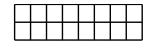

5

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

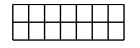

4

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-}

-Graphics-

1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

4

{-Graphics-,-Graphics-,-Graphics-}

-Graphics-

1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-}

-Graphics-

1

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

2

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

3

{-Graphics-,-Graphics-,-Graphics-,-Graphics-}

-Graphics-

4

```mathematica
MinList={{{0,0,0,0},2},{{-1/2,-1/2,0,0},0},{{-1/2,-1/2,-1/2,-1/2},0},{{-1/2,-1/2,-1/2,1/2},1},{{-1,-1,-1,-1},0},{{-1,-1,1,1},0},{{-1,-1,-1/2,-1/2},0},{{-1,-1,-1/2,1/2},1}};
stateList=Join@@Table[MapAt[#+2n&,MinList,{All,2}],{n,0,2}]//Sort
GenerateTable[stateList]
```

```mathematica
LorentzCount[Model,("Q1")^3("Q2")^3("Q3")^3"L1""L2""L3"]
GaugeCount[Model,"SU3c",("Q1")^3("Q2")^3("Q3")^3"L1""L2""L3"]
GaugeCount[Model,"SU2w",("Q1")^3("Q2")^3("Q3")^3"L1""L2""L3"]
Type2TermsCount[Model,("Q1")^3("Q2")^3("Q3")^3"L1""L2""L3"]
```

<|{Q1→{3},Q2→{3},Q3→{3}}→8,{Q1→{3},Q2→{3},Q3→{2,1}}→6,{Q1→{3},Q2→{2,1},Q3→{3}}→6,{Q1→{3},Q2→{2,1},Q3→{2,1}}→4,{Q1→{2,1},Q2→{3},Q3→{3}}→6,{Q1→{2,1},Q2→{3},Q3→{2,1}}→4,{Q1→{2,1},Q2→{2,1},Q3→{3}}→4,{Q1→{2,1},Q2→{2,1},Q3→{2,1}}→5|>

<|{Q1→{3},Q2→{3},Q3→{3}}→1,{Q1→{3},Q2→{2,1},Q3→{2,1}}→1,{Q1→{2,1},Q2→{3},Q3→{2,1}}→1,{Q1→{2,1},Q2→{2,1},Q3→{3}}→1,{Q1→{2,1},Q2→{2,1},Q3→{2,1}}→2,{Q1→{2,1},Q2→{2,1},Q3→{1,1,1}}→1,{Q1→{2,1},Q2→{1,1,1},Q3→{2,1}}→1,{Q1→{1,1,1},Q2→{2,1},Q3→{2,1}}→1,{Q1→{1,1,1},Q2→{1,1,1},Q3→{1,1,1}}→1|>

<|{Q1→{3},Q2→{3},Q3→{3}}→8,{Q1→{3},Q2→{3},Q3→{2,1}}→6,{Q1→{3},Q2→{2,1},Q3→{3}}→6,{Q1→{3},Q2→{2,1},Q3→{2,1}}→4,{Q1→{2,1},Q2→{3},Q3→{3}}→6,{Q1→{2,1},Q2→{3},Q3→{2,1}}→4,{Q1→{2,1},Q2→{2,1},Q3→{3}}→4,{Q1→{2,1},Q2→{2,1},Q3→{2,1}}→5|>

<|{Q1→{3},Q2→{3},Q3→{3}}→3486|>

```mathematica
W2Diagonalize[{1/2,1/2,1/2,1/2},2,{1,3}]
```

<|j→{2,1,0},transfer→(-6 | -1 | 6
0 | -1 | 2
0 | 1 | 0),j-basis→{-[13]_^ [24]_^ s_24^-6 [13]_^ [24]_^ s_34^+6 [12]_^ [34]_^ s_34^,-[13]_^ [24]_^ s_24^-2 [13]_^ [24]_^ s_34^,[13]_^ [24]_^ s_24^}|>

```mathematica
W2Diagonalize[{1/2,1/2,1/2,1/2},2,{1,3},OutputFormat->"working"];
j2amp=%["j-basis"]⟦1⟧;
reduce[W2[j2amp,{1,3}]+6Mandelstam[{1,3}]j2amp,4]//Simplify
```

0

```mathematica
PrintStat[Model,8]
```

-----------------------

Enumerating dim 8 operators ...

--- find all types (time: 6.81762)

number of complex types: 304

number of real types: 541

number of complex terms: 714

number of real terms: 1266

number of complex operators: 25248

number of real operators: 44807

total time: 7.920715

```mathematica
OpBasisD6=GenerateOperatorList[Model,6,T2TOptions->{FerCom->4}]
```

Generating types of operators ...

Evaluating class:  (/9)

Time spent: 4.87681

<|FL^3→<|GL^3→<|{}→{f_^ABCSubsuperscriptBox[GL, , A]_μν^SubsuperscriptBox[GL, , C]_^νλSubsuperscriptBox[SubsuperscriptBox[GL, , B], , μ]_λ^}|>,WL^3→<|{}→{ϵ_^IJKSubsuperscriptBox[WL, , I]_μν^SubsuperscriptBox[WL, , K]_^νλSubsuperscriptBox[SubsuperscriptBox[WL, , J], , μ]_λ^}|>|>,ψ^4→<|L Q^3→<|{Q→{3},L→{1}}→{ϵ_^abcϵ_^ikϵ_^jl (SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[q, r, ]_aj^) (SubsuperscriptBox[q, s, ]_bk^ C SubsuperscriptBox[q, t, ]_cl^)},{Q→{2,1},L→{1}}→{ϵ_^abcϵ_^ikϵ_^jl (SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[q, r, ]_aj^) (SubsuperscriptBox[q, s, ]_bk^ C SubsuperscriptBox[q, t, ]_cl^)},{Q→{1,1,1},L→{1}}→{ϵ_^abcϵ_^ikϵ_^jl (SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[q, r, ]_aj^) (SubsuperscriptBox[q, s, ]_bk^ C SubsuperscriptBox[q, t, ]_cl^)}|>,dc Q^2 uc→<|{Q→{2},dc→{1},uc→{1}}→{ϵ_^ij (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, r, ]_bi^) (SubsuperscriptBox[OverscriptBox[u, _], t, ]_^b SubsuperscriptBox[q, s, ]_aj^),ϵ_^ij (SubsuperscriptBox[OverscriptBox[u, _], t, ]_^b SubsuperscriptBox[q, r, ]_bi^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, s, ]_aj^)},{Q→{1,1},dc→{1},uc→{1}}→{ϵ_^ij (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, r, ]_bi^) (SubsuperscriptBox[OverscriptBox[u, _], t, ]_^b SubsuperscriptBox[q, s, ]_aj^),ϵ_^ij (SubsuperscriptBox[OverscriptBox[u, _], t, ]_^b SubsuperscriptBox[q, r, ]_bi^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, s, ]_aj^)}|>,ec L Q uc→<|{}→{ϵ_^ij (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ SubsuperscriptBox[l, r, ]_i^) (SubsuperscriptBox[OverscriptBox[u, _], t, ]_^a SubsuperscriptBox[q, s, ]_aj^),ϵ_^ij (SubsuperscriptBox[OverscriptBox[u, _], t, ]_^a SubsuperscriptBox[l, r, ]_i^) (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ SubsuperscriptBox[q, s, ]_aj^)}|>,dc ec uc^2→<|{uc→{2},dc→{1},ec→{1}}→{ϵ_abc^ (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[u, _], s, ]_^b) (SubsuperscriptBox[OverscriptBox[e, _], r, ]_^ C SubsuperscriptBox[OverscriptBox[u, _], t, ]_^c)},{uc→{1,1},dc→{1},ec→{1}}→{ϵ_abc^ (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[e, _], r, ]_^) (SubsuperscriptBox[OverscriptBox[u, _], s, ]_^b C SubsuperscriptBox[OverscriptBox[u, _], t, ]_^c)}|>|>,FL ϕ ψ^2→<|GL H Q uc→<|{}→{ⅈ SubsuperscriptBox[λ, , A]_b^aϵ_^ijH_j^SubsuperscriptBox[GL, , A]_^μν (SubsuperscriptBox[OverscriptBox[u, _], r, ]_^b σ_μ_ν SubsuperscriptBox[q, p, ]_ai^)}|>,dc GL H† Q→<|{}→{ⅈ SubsuperscriptBox[λ, , A]_a^b(H†)_^iSubsuperscriptBox[GL, , A]_^μν (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a σ_μ_ν SubsuperscriptBox[q, r, ]_bi^)}|>,H Q uc WL→<|{}→{-ⅈ SubsuperscriptBox[τ, , I]_l^jϵ_^ilH_j^SubsuperscriptBox[WL, , I]_^μν (SubsuperscriptBox[OverscriptBox[u, _], r, ]_^a σ_μ_ν SubsuperscriptBox[q, p, ]_ai^)}|>,dc H† Q WL→<|{}→{ⅈ SubsuperscriptBox[τ, , I]_j^i(H†)_^jSubsuperscriptBox[WL, , I]_^μν (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a σ_μ_ν SubsuperscriptBox[q, r, ]_ai^)}|>,ec H† L WL→<|{}→{ⅈ SubsuperscriptBox[τ, , I]_j^i(H†)_^jSubsuperscriptBox[WL, , I]_^μν (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ σ_μ_ν SubsuperscriptBox[l, r, ]_i^)}|>,BL H Q uc→<|{}→{ⅈ ϵ_^ijH_j^SubsuperscriptBox[BL, , ]_^μν (SubsuperscriptBox[OverscriptBox[u, _], r, ]_^a σ_μ_ν SubsuperscriptBox[q, p, ]_ai^)}|>,BL dc H† Q→<|{}→{ⅈ (H†)_^iSubsuperscriptBox[BL, , ]_^μν (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a σ_μ_ν SubsuperscriptBox[q, r, ]_ai^)}|>,BL ec H† L→<|{}→{ⅈ (H†)_^iSubsuperscriptBox[BL, , ]_^μν (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ σ_μ_ν SubsuperscriptBox[l, r, ]_i^)}|>|>,FL^2 ϕ^2→<|GL^2 H H†→<|{}→{H_i^(H†)_^iSubsuperscriptBox[GL, , A]_μν^SubsuperscriptBox[GL, , A]_^μν}|>,H H† WL^2→<|{}→{H_i^(H†)_^iSubsuperscriptBox[WL, , I]_μν^SubsuperscriptBox[WL, , I]_^μν}|>,BL H H† WL→<|{}→{SubsuperscriptBox[τ, , I]_j^iH_i^(H†)_^jSubsuperscriptBox[BL, , ]_μν^SubsuperscriptBox[WL, , I]_^μν}|>,BL^2 H H†→<|{}→{H_i^(H†)_^iSubsuperscriptBox[BL, , ]_μν^SubsuperscriptBox[BL, , ]_^μν}|>|>,ψ^2 (ψ̄)^2→<|Q^2 (Q†)^2→<|{Q→{2},Q†→{2}}→{(SubsuperscriptBox[OverscriptBox[q, _], s, ]_^ai C SubsuperscriptBox[OverscriptBox[q, _], t, ]_^bj) (SubsuperscriptBox[q, p, ]_ai^ C SubsuperscriptBox[q, r, ]_bj^),(SubsuperscriptBox[OverscriptBox[q, _], s, ]_^aj C SubsuperscriptBox[OverscriptBox[q, _], t, ]_^bi) (SubsuperscriptBox[q, p, ]_ai^ C SubsuperscriptBox[q, r, ]_bj^)},{Q→{1,1},Q†→{1,1}}→{(SubsuperscriptBox[OverscriptBox[q, _], s, ]_^ai C SubsuperscriptBox[OverscriptBox[q, _], t, ]_^bj) (SubsuperscriptBox[q, p, ]_ai^ C SubsuperscriptBox[q, r, ]_bj^),(SubsuperscriptBox[OverscriptBox[q, _], s, ]_^aj C SubsuperscriptBox[OverscriptBox[q, _], t, ]_^bi) (SubsuperscriptBox[q, p, ]_ai^ C SubsuperscriptBox[q, r, ]_bj^)}|>,ec† Q^2 uc†→<|{Q→{2},ec†→{1},uc†→{1}}→{ϵ_^abcϵ_^ij (SubsuperscriptBox[q, p, ]_ai^ C SubsuperscriptBox[q, r, ]_bj^) (SubsuperscriptBox[e, s, ]_^ C SubsuperscriptBox[u, t, ]_c^)}|>,Q Q† uc uc†→<|{}→{(SubsuperscriptBox[OverscriptBox[u, _], r, ]_^a SubsuperscriptBox[q, p, ]_ai^) (SubsuperscriptBox[OverscriptBox[q, _], s, ]_^ci SubsuperscriptBox[u, t, ]_c^),(SubsuperscriptBox[OverscriptBox[u, _], r, ]_^b SubsuperscriptBox[q, p, ]_ai^) (SubsuperscriptBox[OverscriptBox[q, _], s, ]_^ai SubsuperscriptBox[u, t, ]_b^)}|>,dc dc† Q Q†→<|{}→{(SubsuperscriptBox[OverscriptBox[q, _], t, ]_^bi SubsuperscriptBox[d, s, ]_a^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, r, ]_bi^),(SubsuperscriptBox[OverscriptBox[q, _], t, ]_^ci SubsuperscriptBox[d, s, ]_c^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, r, ]_ai^)}|>,dc ec† L† Q→<|{}→{(SubsuperscriptBox[OverscriptBox[l, _], t, ]_^i SubsuperscriptBox[e, s, ]_^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, r, ]_ai^)}|>,L L† Q Q†→<|{}→{(SubsuperscriptBox[OverscriptBox[l, _], s, ]_^i C SubsuperscriptBox[OverscriptBox[q, _], t, ]_^aj) (SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[q, r, ]_aj^),(SubsuperscriptBox[OverscriptBox[l, _], s, ]_^j C SubsuperscriptBox[OverscriptBox[q, _], t, ]_^ai) (SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[q, r, ]_aj^)}|>,dc† L Q uc†→<|{}→{-ϵ_^abcϵ_^ij (SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[q, r, ]_aj^) (SubsuperscriptBox[d, s, ]_b^ C SubsuperscriptBox[u, t, ]_c^)}|>,ec ec† Q Q†→<|{}→{(SubsuperscriptBox[OverscriptBox[q, _], t, ]_^ai SubsuperscriptBox[e, s, ]_^) (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ SubsuperscriptBox[q, r, ]_ai^)}|>,uc^2 (uc†)^2→<|{uc→{2},uc†→{2}}→{(SubsuperscriptBox[OverscriptBox[u, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[u, _], r, ]_^b) (SubsuperscriptBox[u, s, ]_a^ C SubsuperscriptBox[u, t, ]_b^)},{uc→{1,1},uc†→{1,1}}→{(SubsuperscriptBox[OverscriptBox[u, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[u, _], r, ]_^b) (SubsuperscriptBox[u, s, ]_a^ C SubsuperscriptBox[u, t, ]_b^)}|>,dc dc† uc uc†→<|{}→{(SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[u, _], r, ]_^b) (SubsuperscriptBox[d, s, ]_a^ C SubsuperscriptBox[u, t, ]_b^),(SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[u, _], r, ]_^b) (SubsuperscriptBox[d, s, ]_b^ C SubsuperscriptBox[u, t, ]_a^)}|>,L L† uc uc†→<|{}→{(SubsuperscriptBox[OverscriptBox[u, _], r, ]_^a SubsuperscriptBox[l, p, ]_i^) (SubsuperscriptBox[OverscriptBox[l, _], s, ]_^i SubsuperscriptBox[u, t, ]_a^)}|>,ec ec† uc uc†→<|{}→{(SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ C SubsuperscriptBox[OverscriptBox[u, _], r, ]_^a) (SubsuperscriptBox[e, s, ]_^ C SubsuperscriptBox[u, t, ]_a^)}|>,dc^2 (dc†)^2→<|{dc→{2},dc†→{2}}→{(SubsuperscriptBox[d, s, ]_a^ C SubsuperscriptBox[d, t, ]_b^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[d, _], r, ]_^b)},{dc→{1,1},dc†→{1,1}}→{(SubsuperscriptBox[d, s, ]_a^ C SubsuperscriptBox[d, t, ]_b^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[d, _], r, ]_^b)}|>,dc dc† L L†→<|{}→{(SubsuperscriptBox[OverscriptBox[l, _], t, ]_^i SubsuperscriptBox[d, s, ]_a^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[l, r, ]_i^)}|>,dc dc† ec ec†→<|{}→{(SubsuperscriptBox[d, s, ]_a^ C SubsuperscriptBox[e, t, ]_^) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a C SubsuperscriptBox[OverscriptBox[e, _], r, ]_^)}|>,L^2 (L†)^2→<|{L→{2},L†→{2}}→{(SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[l, r, ]_j^) (SubsuperscriptBox[OverscriptBox[l, _], s, ]_^i C SubsuperscriptBox[OverscriptBox[l, _], t, ]_^j)},{L→{1,1},L†→{1,1}}→{(SubsuperscriptBox[l, p, ]_i^ C SubsuperscriptBox[l, r, ]_j^) (SubsuperscriptBox[OverscriptBox[l, _], s, ]_^i C SubsuperscriptBox[OverscriptBox[l, _], t, ]_^j)}|>,ec ec† L L†→<|{}→{(SubsuperscriptBox[OverscriptBox[l, _], t, ]_^i SubsuperscriptBox[e, s, ]_^) (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ SubsuperscriptBox[l, r, ]_i^)}|>,ec^2 (ec†)^2→<|{ec→{2},ec†→{2}}→{(SubsuperscriptBox[e, s, ]_^ C SubsuperscriptBox[e, t, ]_^) (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ C SubsuperscriptBox[OverscriptBox[e, _], r, ]_^)}|>|>,D ϕ^2 ψ ψ̄→<|D H H† Q Q†→<|{}→{-ⅈ H_j^ (D^μ (H†)_^i) (SubsuperscriptBox[OverscriptBox[q, _], r, ]_^aj σ_μ SubsuperscriptBox[q, p, ]_ai^),-ⅈ H_j^ (D^μ (H†)_^j) (SubsuperscriptBox[OverscriptBox[q, _], r, ]_^ai σ_μ SubsuperscriptBox[q, p, ]_ai^)}|>,D dc† H^2 uc→<|{uc→{1},dc†→{1}}→{ⅈ ϵ_^ijH_i^ (D^μ H_j^) (SubsuperscriptBox[OverscriptBox[u, _], p, ]_^a σ_μ SubsuperscriptBox[d, r, ]_a^)}|>,D H H† uc uc†→<|{}→{ⅈ H_i^ (D^μ (H†)_^i) (SubsuperscriptBox[OverscriptBox[u, _], p, ]_^a σ_μ SubsuperscriptBox[u, r, ]_a^)}|>,D dc dc† H H†→<|{}→{ⅈ H_i^ (D^μ (H†)_^i) (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a σ_μ SubsuperscriptBox[d, r, ]_a^)}|>,D H H† L L†→<|{}→{-ⅈ H_j^ (D^μ (H†)_^i) (SubsuperscriptBox[OverscriptBox[l, _], r, ]_^j σ_μ SubsuperscriptBox[l, p, ]_i^),-ⅈ H_j^ (D^μ (H†)_^j) (SubsuperscriptBox[OverscriptBox[l, _], r, ]_^i σ_μ SubsuperscriptBox[l, p, ]_i^)}|>,D ec ec† H H†→<|{}→{ⅈ H_i^ (D^μ (H†)_^i) (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ σ_μ SubsuperscriptBox[e, r, ]_^)}|>|>,D^2 ϕ^4→<|D^2 H^2 (H†)^2→<|{}→{H_i^H_j^ (D_μ (H†)_^i) (D^μ (H†)_^j),H_i^H_j^ (D^μ (H†)_^i) (D_μ (H†)_^j)}|>|>,ϕ^3 ψ^2→<|H^2 H† Q uc→<|{Q→{1},uc→{1}}→{-ϵ_^ikH_j^H_k^(H†)_^j (SubsuperscriptBox[OverscriptBox[u, _], r, ]_^a SubsuperscriptBox[q, p, ]_ai^)}|>,dc H (H†)^2 Q→<|{dc→{1},Q→{1}}→{H_j^(H†)_^i(H†)_^j (SubsuperscriptBox[OverscriptBox[d, _], p, ]_^a SubsuperscriptBox[q, r, ]_ai^)}|>,ec H (H†)^2 L→<|{ec→{1},L→{1}}→{H_j^(H†)_^i(H†)_^j (SubsuperscriptBox[OverscriptBox[e, _], p, ]_^ SubsuperscriptBox[l, r, ]_i^)}|>|>,ϕ^6→<|H^3 (H†)^3→<|{}→{H_i^H_j^H_k^(H†)_^i(H†)_^j(H†)_^k}|>|>|>

```mathematica
AmpBasisD7=GenerateOperatorList[Model,7,T2TOptions->{OutputFormat->"amplitude"}]
```

Generating types of operators ...

Evaluating class:  (/15)

Time spent: 4.10634

<|D ψ^3 ψ̄→<|D dc^3 ec†→<|{dc→{3},ec†→{1}}→{(<13>)_^(<23>)_^[34]_^ϵ_abc^}|>,D dc^2 L Q†→<|{dc→{2},L→{1},Q†→{1}}→{(<13>)_^(<23>)_^[34]_^δ_j^iϵ_abc^}|>,D dc L^2 uc†→<|{L→{2},dc→{1},uc†→{1}}→{(<13>)_^(<23>)_^[34]_^δ_a^bϵ_^ij}|>|>,D^2 ϕ^2 ψ^2→<|D^2 H^2 L^2→<|{L→{2}}→{-(<12>)_^s_34^ϵ_^ikϵ_^jl,-(<12>)_^s_34^ϵ_^ijϵ_^kl}|>|>,ϕ ψ^4→<|dc H L^2 Q→<|{L→{1,1},dc→{1},Q→{1}}→{-(<12>)_^(<34>)_^δ_a^bϵ_^ikϵ_^jl,-(<13>)_^(<24>)_^δ_a^bϵ_^ikϵ_^jl},{L→{2},dc→{1},Q→{1}}→{-(<12>)_^(<34>)_^δ_a^bϵ_^ikϵ_^jl,-(<13>)_^(<24>)_^δ_a^bϵ_^ikϵ_^jl}|>,dc^2 H L uc→<|{dc→{2},L→{1},uc→{1}}→{-(<13>)_^(<24>)_^ϵ_abc^ϵ_^ij},{dc→{1,1},L→{1},uc→{1}}→{-(<12>)_^(<34>)_^ϵ_abc^ϵ_^ij}|>,dc^3 H† L→<|{dc→{2,1},L→{1}}→{(<12>)_^(<34>)_^δ_j^iϵ_abc^}|>,ec H L^3→<|{L→{3},ec→{1}}→{-(<12>)_^(<34>)_^ϵ_^ikϵ_^jl},{L→{2,1},ec→{1}}→{-(<12>)_^(<34>)_^ϵ_^ikϵ_^jl},{L→{1,1,1},ec→{1}}→{-(<12>)_^(<34>)_^ϵ_^ikϵ_^jl}|>|>,FL ϕ^2 ψ^2→<|H^2 L^2 WL→<|{L→{1,1}}→{-(<12>)_^(<13>)_^SubsuperscriptBox[τ, , I]_n^kϵ_^ilϵ_^jn},{L→{2}}→{-(<12>)_^(<13>)_^SubsuperscriptBox[τ, , I]_n^kϵ_^ilϵ_^jn}|>,BL H^2 L^2→<|{L→{1,1}}→{(<12>)_^(<13>)_^ϵ_^ikϵ_^jl}|>|>,ϕ ψ^2 (ψ̄)^2→<|dc† H† L† Q^2→<|{Q→{1,1},dc†→{1},L†→{1}}→{(<12>)_^[45]_^δ_k^iδ_l^jϵ_^abc},{Q→{2},dc†→{1},L†→{1}}→{(<12>)_^[45]_^δ_k^iδ_l^jϵ_^abc}|>,H† (L†)^2 Q uc→<|{L†→{2},Q→{1},uc→{1}}→{(<12>)_^[45]_^δ_b^aδ_k^iϵ_jl^},{L†→{1,1},Q→{1},uc→{1}}→{(<12>)_^[45]_^δ_b^aδ_k^iϵ_jl^}|>,(dc†)^2 ec H† Q→<|{dc†→{1,1},ec→{1},Q→{1}}→{(<12>)_^[45]_^δ_j^iϵ_^abc}|>,dc† ec H† L† uc→<|{}→{(<12>)_^[45]_^δ_a^bϵ_ij^}|>|>,D ϕ^3 ψ ψ̄→<|D ec† H^3 L→<|{L→{1},ec†→{1}}→{-(<14>)_^[45]_^ϵ_^ikϵ_^jl}|>|>,ϕ^4 ψ^2→<|H^3 H† L^2→<|{L→{2}}→{(<12>)_^δ_n^kϵ_^ilϵ_^jm}|>|>|>

```mathematica
Nest[StringReplace[a___~~"\!\(\*SubsuperscriptBox[\(H\), \("~~x_~~"\), \(\)]\)"~~y___~~"\!\(\*SubsuperscriptBox[\(H†\), \(\), \("~~x_~~"\)]\)"~~b___:>a~~"|H\!\(\*SuperscriptBox[\(|\), \(2\)]\)" ~~y~~b],"H_i^H_j^H_k^(H†)_^i(H†)_^j(H†)_^k",3]
```

|H|^2|H|^2|H|^2

#### Other Model

```mathematica
LEFTFUND={"i","j","k","l","m","n"};
RIGHTFUND={"ī","j̄","k̄","l̄","m̄","n̄"};
LEFTADJ={"I","J","K"};
RIGHTADJ={"Ī","J̄","K̄"};
```

```mathematica
(* Define New Model *)
Clear[DefModel];
SetAttributes[DefModel,HoldFirst];
DefModel[model_]:=Module[{},
model=<|"Global"->{},"rep2ind"-><||>,"rep2indOut"-><||>|>;
AddGroup[model,"SU2l","U",{},<|{0}->{Function[x,Nothing],{}},{1}->{a,LEFTFUND},{2}->{A,LEFTADJ}|>];
AddGroup[model,"SU2r","V",{},<|{0}->{Function[x,Nothing],{}},{1}->{a,RIGHTFUND},{2}->{A,RIGHTADJ}|>];
AddField[model,"ql",-1/2,{{1},{0}},{},Chirality->{"ql","left"}];
AddField[model,"qr",-1/2,{{0},{1}},{},Chirality->{"qr","right"}];
AddField[model,"Hl",0,{{1},{0}},{}];
AddField[model,"Hr",0,{{0},{1}},{}]
]
```

```mathematica
DefModel[Model];
```

```mathematica
tensortooper[-chψ[Subscript[ψ,1],1,Subscript[ψ,3]] chψ[Subscript[ψ,2],1,Subscript[ψ,4]]]
tensortooper[-2 Subscript[ϕ,1] Subscript[ϕ,2] Subscript[ϕ,3] Subscript[ϕ,4] TensorContract[de[2]⊗de[4],{{1,2}}]]
tensortooper[2 Subscript[ϕ,3] Subscript[ϕ,4] TensorContract[F[1]⊗F[2],{{1,3},{2,4}}]]
tensortooper[4 TensorContract[F[1]⊗F[2]⊗F[3],{{1,3},{2,5},{4,6}}]]
```

-chψ[ψ_1,1,ψ_3] chψ[ψ_2,1,ψ_4]

-2 ϕ_1 ϕ_2 ϕ_3 ϕ_4 D_2_μ D_4^μ

2 ϕ_3 ϕ_4 FL_1[down,μ,down,ν] FL_2[up,μ,up,ν]

4 FL_1[down,μ,down,ν] FL_2[up,μ,down,λ] FL_3[up,ν,up,λ]

```mathematica
GenerateOperatorList[Model,6]
```

Generating types of operators ...

Evaluating class:  (/9)

Time spent: 17.947405

<|FL^3→<|UL^3→<|{}→{SubsuperscriptBox[SubsuperscriptBox[UL, , J], , μ]_λ^ SubsuperscriptBox[UL, , I]_μν^ SubsuperscriptBox[UL, , K]_^νλ ϵ_^IJK}|>,VL^3→<|{}→{SubsuperscriptBox[SubsuperscriptBox[VL, , OverscriptBox[J, _]], , μ]_λ^ SubsuperscriptBox[VL, , OverscriptBox[I, _]]_μν^ SubsuperscriptBox[VL, , OverscriptBox[K, _]]_^νλ ϵ_^(OverscriptBox[I, _]OverscriptBox[J, _]OverscriptBox[K, _])}|>|>,ψ^4→<|ql^4→<|{}→{ϵ_^ik ϵ_^jl (ql_i^ ql_j^) (ql_k^ ql_l^)}|>,ql^2 qr^2→<|{}→{ϵ_^ij ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (ql_i^ qr_OverscriptBox[i, _]^) (ql_j^ qr_OverscriptBox[j, _]^)}|>,qr^4→<|{}→{ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) ϵ_^(OverscriptBox[j, _]OverscriptBox[l, _]) (qr_OverscriptBox[i, _]^ qr_OverscriptBox[j, _]^) (qr_OverscriptBox[k, _]^ qr_OverscriptBox[l, _]^)}|>|>,FL ϕ ψ^2→<||>,FL^2 ϕ^2→<|Hl Hl† UL^2→<|{}→{Hl_i^ (Hl†)_^i SubsuperscriptBox[UL, , I]_^μν SubsuperscriptBox[UL, , I]_μν^}|>,Hr Hr† UL^2→<|{}→{Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _] SubsuperscriptBox[UL, , I]_^μν SubsuperscriptBox[UL, , I]_μν^}|>,Hl Hl† VL^2→<|{}→{Hl_i^ (Hl†)_^i SubsuperscriptBox[VL, , OverscriptBox[I, _]]_^μν SubsuperscriptBox[VL, , OverscriptBox[I, _]]_μν^}|>,Hr Hr† VL^2→<|{}→{Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _] SubsuperscriptBox[VL, , OverscriptBox[I, _]]_^μν SubsuperscriptBox[VL, , OverscriptBox[I, _]]_μν^}|>|>,ψ^2 (ψ̄)^2→<|ql^2 (ql†)^2→<|{}→{(ql_i^ ql_j^) ((ql†)_^i (ql†)_^j)}|>,ql ql† qr qr†→<|{}→{(ql_i^ qr_OverscriptBox[i, _]^) ((ql†)_^i (qr†)_^OverscriptBox[i, _])}|>,qr^2 (qr†)^2→<|{}→{(qr_OverscriptBox[i, _]^ qr_OverscriptBox[j, _]^) ((qr†)_^OverscriptBox[i, _] (qr†)_^OverscriptBox[j, _])}|>|>,D ϕ^2 ψ ψ̄→<|D Hl^2 ql ql†→<|{}→{-ⅈ Hl_j^ ϵ_^ik (D^μ Hl_k^) (ql_i^ σ_μ (ql†)_^j)}|>,D Hl Hl† ql ql†→<|{}→{ⅈ Hl_j^ (D^μ (Hl†)_^i) (ql_i^ σ_μ (ql†)_^j),ⅈ Hl_j^ (D^μ (Hl†)_^j) (ql_i^ σ_μ (ql†)_^i)}|>,D Hl Hr ql qr†→<|{}→{-ⅈ Hl_j^ ϵ_^ij (D^μ Hr_OverscriptBox[i, _]^) (ql_i^ σ_μ (qr†)_^OverscriptBox[i, _])}|>,D Hl Hr† ql qr†→<|{}→{-ⅈ Hl_j^ ϵ_^ij ϵ_(OverscriptBox[i, _]OverscriptBox[j, _])^ (D^μ (Hr†)_^OverscriptBox[i, _]) (ql_i^ σ_μ (qr†)_^OverscriptBox[j, _])}|>,D Hl† Hr ql qr†→<|{}→{ⅈ (Hl†)_^i (D^μ Hr_OverscriptBox[i, _]^) (ql_i^ σ_μ (qr†)_^OverscriptBox[i, _])}|>,D Hl† Hr† ql qr†→<|{}→{ⅈ (Hl†)_^i ϵ_(OverscriptBox[i, _]OverscriptBox[j, _])^ (D^μ (Hr†)_^OverscriptBox[i, _]) (ql_i^ σ_μ (qr†)_^OverscriptBox[j, _])}|>,D Hr^2 ql ql†→<|{}→{ⅈ Hr_OverscriptBox[i, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (D^μ Hr_OverscriptBox[j, _]^) (ql_i^ σ_μ (ql†)_^i)}|>,D Hr Hr† ql ql†→<|{}→{ⅈ Hr_OverscriptBox[i, _]^ (D^μ (Hr†)_^OverscriptBox[i, _]) (ql_i^ σ_μ (ql†)_^i)}|>,D Hl^2 qr qr†→<|{}→{ⅈ Hl_i^ ϵ_^ij (D^μ Hl_j^) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[i, _])}|>,D Hl Hl† qr qr†→<|{}→{ⅈ Hl_i^ (D^μ (Hl†)_^i) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[i, _])}|>,D Hr^2 qr qr†→<|{}→{-ⅈ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) (D^μ Hr_OverscriptBox[k, _]^) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[j, _])}|>,D Hr Hr† qr qr†→<|{}→{ⅈ Hr_OverscriptBox[j, _]^ (D^μ (Hr†)_^OverscriptBox[i, _]) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[j, _]),ⅈ Hr_OverscriptBox[j, _]^ (D^μ (Hr†)_^OverscriptBox[j, _]) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[i, _])}|>|>,D^2 ϕ^4→<|D^2 Hl^4→<|{}→{Hl_i^ Hl_j^ ϵ_^ik ϵ_^jl (D_μ Hl_k^) (D^μ Hl_l^)}|>,D^2 Hl^3 Hl†→<|{}→{Hl_i^ Hl_j^ ϵ_^ik (D_μ Hl_k^) (D^μ (Hl†)_^j)}|>,D^2 Hl^2 (Hl†)^2→<|{}→{Hl_i^ Hl_j^ (D_μ (Hl†)_^i) (D^μ (Hl†)_^j),Hl_i^ (Hl†)_^i (D_μ Hl_j^) (D^μ (Hl†)_^j)}|>,D^2 Hl^2 Hr^2→<|{}→{Hl_i^ Hr_OverscriptBox[i, _]^ ϵ_^ij ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (D_μ Hl_j^) (D^μ Hr_OverscriptBox[j, _]^)}|>,D^2 Hl^2 Hr Hr†→<|{}→{Hl_i^ Hr_OverscriptBox[i, _]^ ϵ_^ij (D_μ Hl_j^) (D^μ (Hr†)_^OverscriptBox[i, _])}|>,D^2 Hl^2 (Hr†)^2→<|{}→{Hl_i^ (Hr†)_^OverscriptBox[i, _] ϵ_^ij ϵ_(OverscriptBox[i, _]OverscriptBox[j, _])^ (D_μ Hl_j^) (D^μ (Hr†)_^OverscriptBox[j, _])}|>,D^2 Hl Hl† Hr^2→<|{}→{Hl_i^ Hr_OverscriptBox[i, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (D_μ (Hl†)_^i) (D^μ Hr_OverscriptBox[j, _]^)}|>,D^2 Hl Hl† Hr Hr†→<|{}→{Hl_i^ (Hl†)_^i (D_μ Hr_OverscriptBox[i, _]^) (D^μ (Hr†)_^OverscriptBox[i, _]),Hl_i^ Hr_OverscriptBox[i, _]^ (D_μ (Hl†)_^i) (D^μ (Hr†)_^OverscriptBox[i, _])}|>,D^2 Hr^4→<|{}→{Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) ϵ_^(OverscriptBox[j, _]OverscriptBox[l, _]) (D_μ Hr_OverscriptBox[k, _]^) (D^μ Hr_OverscriptBox[l, _]^)}|>,D^2 Hr^3 Hr†→<|{}→{Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) (D_μ Hr_OverscriptBox[k, _]^) (D^μ (Hr†)_^OverscriptBox[j, _])}|>,D^2 Hr^2 (Hr†)^2→<|{}→{Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ (D_μ (Hr†)_^OverscriptBox[i, _]) (D^μ (Hr†)_^OverscriptBox[j, _]),Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _] (D_μ Hr_OverscriptBox[j, _]^) (D^μ (Hr†)_^OverscriptBox[j, _])}|>|>,ϕ^3 ψ^2→<||>,ϕ^6→<|Hl^3 (Hl†)^3→<|{}→{Hl_i^ Hl_j^ Hl_k^ (Hl†)_^i (Hl†)_^j (Hl†)_^k}|>,Hl^2 (Hl†)^2 Hr Hr†→<|{}→{Hl_i^ Hl_j^ (Hl†)_^i (Hl†)_^j Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _]}|>,Hl Hl† Hr^2 (Hr†)^2→<|{}→{Hl_i^ (Hl†)_^i Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ (Hr†)_^OverscriptBox[i, _] (Hr†)_^OverscriptBox[j, _]}|>,Hr^3 (Hr†)^3→<|{}→{Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ Hr_OverscriptBox[k, _]^ (Hr†)_^OverscriptBox[i, _] (Hr†)_^OverscriptBox[j, _] (Hr†)_^OverscriptBox[k, _]}|>|>|>

```mathematica
Present[%];
```

---------------------
FL^3: 2 type(s)

---------
  1. [UL^3] 1 term(s)

SubsuperscriptBox[SubsuperscriptBox[UL, , J], , μ]_λ^ SubsuperscriptBox[UL, , I]_μν^ SubsuperscriptBox[UL, , K]_^νλ ϵ_^IJK

---------
  2. [VL^3] 1 term(s)

SubsuperscriptBox[SubsuperscriptBox[VL, , OverscriptBox[J, _]], , μ]_λ^ SubsuperscriptBox[VL, , OverscriptBox[I, _]]_μν^ SubsuperscriptBox[VL, , OverscriptBox[K, _]]_^νλ ϵ_^(OverscriptBox[I, _]OverscriptBox[J, _]OverscriptBox[K, _])

---------------------
ψ^4: 3 type(s)

---------
  1. [ql^4] 1 term(s)

ϵ_^ik ϵ_^jl (ql_i^ ql_j^) (ql_k^ ql_l^)

---------
  2. [ql^2 qr^2] 1 term(s)

ϵ_^ij ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (ql_i^ qr_OverscriptBox[i, _]^) (ql_j^ qr_OverscriptBox[j, _]^)

---------
  3. [qr^4] 1 term(s)

ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) ϵ_^(OverscriptBox[j, _]OverscriptBox[l, _]) (qr_OverscriptBox[i, _]^ qr_OverscriptBox[j, _]^) (qr_OverscriptBox[k, _]^ qr_OverscriptBox[l, _]^)

---------------------
FL ϕ ψ^2: 0 type(s)

---------------------
FL^2 ϕ^2: 4 type(s)

---------
  1. [Hl Hl† UL^2] 1 term(s)

-2 Hl_i^ (Hl†)_^i SubsuperscriptBox[UL, , I]_^μν SubsuperscriptBox[UL, , I]_μν^

---------
  2. [Hr Hr† UL^2] 1 term(s)

-2 Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _] SubsuperscriptBox[UL, , I]_^μν SubsuperscriptBox[UL, , I]_μν^

---------
  3. [Hl Hl† VL^2] 1 term(s)

-2 Hl_i^ (Hl†)_^i SubsuperscriptBox[VL, , OverscriptBox[I, _]]_^μν SubsuperscriptBox[VL, , OverscriptBox[I, _]]_μν^

---------
  4. [Hr Hr† VL^2] 1 term(s)

-2 Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _] SubsuperscriptBox[VL, , OverscriptBox[I, _]]_^μν SubsuperscriptBox[VL, , OverscriptBox[I, _]]_μν^

---------------------
ψ^2 (ψ̄)^2: 3 type(s)

---------
  1. [ql^2 (ql†)^2] 1 term(s)

(ql_i^ ql_j^) ((ql†)_^i (ql†)_^j)

---------
  2. [ql ql† qr qr†] 1 term(s)

(ql_i^ qr_OverscriptBox[i, _]^) ((ql†)_^i (qr†)_^OverscriptBox[i, _])

---------
  3. [qr^2 (qr†)^2] 1 term(s)

(qr_OverscriptBox[i, _]^ qr_OverscriptBox[j, _]^) ((qr†)_^OverscriptBox[i, _] (qr†)_^OverscriptBox[j, _])

---------------------
D ϕ^2 ψ ψ̄: 12 type(s)

---------
  1. [D Hl^2 ql ql†] 1 term(s)

-ⅈ Hl_j^ ϵ_^ik (D^μ Hl_k^) (ql_i^ σ_μ (ql†)_^j)

---------
  2. [D Hl Hl† ql ql†] 2 term(s)

ⅈ Hl_j^ (D^μ (Hl†)_^i) (ql_i^ σ_μ (ql†)_^j)

ⅈ Hl_j^ (D^μ (Hl†)_^j) (ql_i^ σ_μ (ql†)_^i)-ⅈ Hl_j^ (D^μ (Hl†)_^i) (ql_i^ σ_μ (ql†)_^j)

---------
  3. [D Hl Hr ql qr†] 1 term(s)

-ⅈ Hl_j^ ϵ_^ij (D^μ Hr_OverscriptBox[i, _]^) (ql_i^ σ_μ (qr†)_^OverscriptBox[i, _])

---------
  4. [D Hl Hr† ql qr†] 1 term(s)

-ⅈ Hl_j^ ϵ_^ij ϵ_(OverscriptBox[i, _]OverscriptBox[j, _])^ (D^μ (Hr†)_^OverscriptBox[i, _]) (ql_i^ σ_μ (qr†)_^OverscriptBox[j, _])

---------
  5. [D Hl† Hr ql qr†] 1 term(s)

ⅈ (Hl†)_^i (D^μ Hr_OverscriptBox[i, _]^) (ql_i^ σ_μ (qr†)_^OverscriptBox[i, _])

---------
  6. [D Hl† Hr† ql qr†] 1 term(s)

ⅈ (Hl†)_^i ϵ_(OverscriptBox[i, _]OverscriptBox[j, _])^ (D^μ (Hr†)_^OverscriptBox[i, _]) (ql_i^ σ_μ (qr†)_^OverscriptBox[j, _])

---------
  7. [D Hr^2 ql ql†] 1 term(s)

ⅈ Hr_OverscriptBox[i, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (D^μ Hr_OverscriptBox[j, _]^) (ql_i^ σ_μ (ql†)_^i)

---------
  8. [D Hr Hr† ql ql†] 1 term(s)

ⅈ Hr_OverscriptBox[i, _]^ (D^μ (Hr†)_^OverscriptBox[i, _]) (ql_i^ σ_μ (ql†)_^i)

---------
  9. [D Hl^2 qr qr†] 1 term(s)

ⅈ Hl_i^ ϵ_^ij (D^μ Hl_j^) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[i, _])

---------
  10. [D Hl Hl† qr qr†] 1 term(s)

ⅈ Hl_i^ (D^μ (Hl†)_^i) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[i, _])

---------
  11. [D Hr^2 qr qr†] 1 term(s)

-ⅈ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) (D^μ Hr_OverscriptBox[k, _]^) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[j, _])

---------
  12. [D Hr Hr† qr qr†] 2 term(s)

ⅈ Hr_OverscriptBox[j, _]^ (D^μ (Hr†)_^OverscriptBox[i, _]) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[j, _])

-ⅈ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) ϵ_(OverscriptBox[k, _]OverscriptBox[l, _])^ (D^μ (Hr†)_^OverscriptBox[k, _]) (qr_OverscriptBox[i, _]^ σ_μ (qr†)_^OverscriptBox[l, _])

---------------------
D^2 ϕ^4: 11 type(s)

---------
  1. [D^2 Hl^4] 1 term(s)

Hl_i^ Hl_j^ ϵ_^ik ϵ_^jl (D_μ Hl_k^) (D^μ Hl_l^)

---------
  2. [D^2 Hl^3 Hl†] 1 term(s)

Hl_i^ Hl_j^ ϵ_^ik (D_μ Hl_k^) (D^μ (Hl†)_^j)

---------
  3. [D^2 Hl^2 (Hl†)^2] 2 term(s)

Hl_i^ Hl_j^ (D_μ (Hl†)_^i) (D^μ (Hl†)_^j)

Hl_i^ (Hl†)_^i (D_μ Hl_j^) (D^μ (Hl†)_^j)

---------
  4. [D^2 Hl^2 Hr^2] 1 term(s)

Hl_i^ Hr_OverscriptBox[i, _]^ ϵ_^ij ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (D_μ Hl_j^) (D^μ Hr_OverscriptBox[j, _]^)

---------
  5. [D^2 Hl^2 Hr Hr†] 1 term(s)

Hl_i^ Hr_OverscriptBox[i, _]^ ϵ_^ij (D_μ Hl_j^) (D^μ (Hr†)_^OverscriptBox[i, _])

---------
  6. [D^2 Hl^2 (Hr†)^2] 1 term(s)

Hl_i^ (Hr†)_^OverscriptBox[i, _] ϵ_^ij ϵ_(OverscriptBox[i, _]OverscriptBox[j, _])^ (D_μ Hl_j^) (D^μ (Hr†)_^OverscriptBox[j, _])

---------
  7. [D^2 Hl Hl† Hr^2] 1 term(s)

Hl_i^ Hr_OverscriptBox[i, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[j, _]) (D_μ (Hl†)_^i) (D^μ Hr_OverscriptBox[j, _]^)

---------
  8. [D^2 Hl Hl† Hr Hr†] 2 term(s)

Hl_i^ (Hl†)_^i (D_μ Hr_OverscriptBox[i, _]^) (D^μ (Hr†)_^OverscriptBox[i, _])

Hl_i^ Hr_OverscriptBox[i, _]^ (D_μ (Hl†)_^i) (D^μ (Hr†)_^OverscriptBox[i, _])

---------
  9. [D^2 Hr^4] 1 term(s)

Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) ϵ_^(OverscriptBox[j, _]OverscriptBox[l, _]) (D_μ Hr_OverscriptBox[k, _]^) (D^μ Hr_OverscriptBox[l, _]^)

---------
  10. [D^2 Hr^3 Hr†] 1 term(s)

Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ ϵ_^(OverscriptBox[i, _]OverscriptBox[k, _]) (D_μ Hr_OverscriptBox[k, _]^) (D^μ (Hr†)_^OverscriptBox[j, _])

---------
  11. [D^2 Hr^2 (Hr†)^2] 2 term(s)

Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ (D_μ (Hr†)_^OverscriptBox[i, _]) (D^μ (Hr†)_^OverscriptBox[j, _])

Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _] (D_μ Hr_OverscriptBox[j, _]^) (D^μ (Hr†)_^OverscriptBox[j, _])

---------------------
ϕ^3 ψ^2: 0 type(s)

---------------------
ϕ^6: 4 type(s)

---------
  1. [Hl^3 (Hl†)^3] 1 term(s)

Hl_i^ Hl_j^ Hl_k^ (Hl†)_^i (Hl†)_^j (Hl†)_^k

---------
  2. [Hl^2 (Hl†)^2 Hr Hr†] 1 term(s)

Hl_i^ Hl_j^ (Hl†)_^i (Hl†)_^j Hr_OverscriptBox[i, _]^ (Hr†)_^OverscriptBox[i, _]

---------
  3. [Hl Hl† Hr^2 (Hr†)^2] 1 term(s)

Hl_i^ (Hl†)_^i Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ (Hr†)_^OverscriptBox[i, _] (Hr†)_^OverscriptBox[j, _]

---------
  4. [Hr^3 (Hr†)^3] 1 term(s)

Hr_OverscriptBox[i, _]^ Hr_OverscriptBox[j, _]^ Hr_OverscriptBox[k, _]^ (Hr†)_^OverscriptBox[i, _] (Hr†)_^OverscriptBox[j, _] (Hr†)_^OverscriptBox[k, _]